# Valid JSON files from AI

```mathematica
datadir="/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/"
```

/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/

```mathematica
exportdocdir="/Volumes/LaCie/BANK/_KAKEN/jsik-cls/"
```

/Volumes/LaCie/BANK/_KAKEN/jsik-cls/

## 背景

```mathematica
kgview=
```

なぜか、オブジェクトをExport[]できない。

## Prompt

添付のデータに対して以下の作業を行って下さい。
 
 - 概要 : 地名候補を地名であるか判定する。
 - 入力データ形式 : json形式、4 つの要素から成る。各要素はさらに配列である可能性がある。
 - 入力データの各要素の説明 : 
  - 第1要素 : 無視して良い
  - 第2要素 : 第4要素から抽出された地名候補
  - 第3要素 : 無視して良い
  - 第4要素 : 文章 （配列）
- 行ってほしい作業 : jsonの第2要素の各地名候補が地名であるかを、第4要素の文脈から判定してほしい。
- 出力データ形式 （判定結果） : 第2要素のみを次のように出力する : 第2要素の地名候補が地名であればそのまま残し、そうでない場合は0に置きかえたもの。

## jemma3

### select第一段階

```mathematica
(gemma3XLS=Import[datadir<>"評価gemma3.xlsx"][[1]])//Length
```

251

```mathematica
(gemma3validline=Cases[gemma3XLS,{_,x_,y_,z_,___}/;(x==1.&&y==1.)||(x==1.&&y==0.&&z==0.)||(x==1.&&y==0.&&z==1.)])//Length
```

152

```mathematica
gemma3validfile=Map[#[[1]]&,gemma3validline];
```

```mathematica
(*Export[datadir<>"gemma3validfile.csv",gemma3validfile,"CSV", "QuotingCharacter"->""]*)
```

### select第二段階

外部で処理
/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutCB/
/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutSL/

### select第三段階

1) コードブロックの抽出

```mathematica
(finevalidfilesgemma["CB"]=(Import[datadir<>"jsonoutCB-gemma3fine.list","CSV"]//Flatten))//Length
```

141

```mathematica
importjsongemma["CB"]=Map[{datadir<>"jsonoutCB/"<>#,Import[datadir<>"jsonoutCB/"<>#,"JSON"]}&,finevalidfilesgemma["CB"]];
```

```mathematica
Map[{Length[#[[2]]],Depth[#[[2]]]}&,importjsongemma["CB"]]
```

{{3,3},{4,4},{4,3},{3,4},{4,3},{4,3},{4,3},{4,3},{4,3},{2,3},{4,3},{3,3},{4,3},{4,3},{4,3},{2,3},{4,3},{4,3},{3,4},{4,3},{4,3},{4,3},{4,3},{4,3},{3,3},{4,3},{4,3},{3,3},{2,3},{4,3},{4,3},{2,3},{4,3},{3,4},{4,3},{4,3},{2,3},{2,3},{3,3},{4,3},{4,3},{4,3},{2,3},{3,4},{2,3},{4,3},{2,3},{4,3},{2,3},{3,4},{3,3},{3,4},{4,3},{4,3},{4,3},{3,3},{3,3},{3,4},{2,3},{4,3},{4,3},{4,3},{2,3},{3,3},{3,3},{3,4},{4,3},{4,3},{3,3},{3,3},{3,4},{4,3},{3,4},{3,3},{4,3},{4,3},{4,3},{4,3},{4,3},{4,3},{4,3},{4,3},{4,3},{4,3},{2,3},{4,3},{2,3},{2,3},{2,3},{4,3},{4,3},{3,3},{3,3},{4,3},{4,3},{3,3},{4,3},{4,3},{4,3},{3,3},{2,3},{4,3},{4,3},{3,3},{3,4},{4,3},{4,3},{3,3},{4,3},{3,3},{2,3},{4,3},{3,3},{4,3},{3,3},{3,3},{4,3},{5,3},{4,3},{3,3},{4,3},{2,3},{4,3},{4,3},{3,4},{4,3},{3,3},{3,3},{2,3},{4,3},{3,3},{2,3},{3,3},{4,3},{4,3},{3,3},{4,3},{4,3},{3,3},{3,3},{2,3}}

```mathematica
exportjsongemma["CB"]=Map[{#[[1]],#[[2,2]]}&,importjsongemma["CB"]];
```

一旦結果をExport[]

```mathematica
(*Map[Export[#[[1]]<>".json",#[[2]]]&,exportjsongemma["CB"]]*)
```

2) シングルラインの抽出

```mathematica
(finevalidfilesgemma["SL"]=(Import[datadir<>"jsonoutSL-gemma3fine.list","CSV"]//Flatten))//Length
```

32

シングルラインのみでしか取れないoutputの確認 -> ないのでこれで終わり。

```mathematica
Complement[finevalidfilesgemma["SL"],finevalidfilesgemma["CB"]]
```

{}

## llama3

### select第一段階

```mathematica
(llama3XLS=Import[datadir<>"評価llama3.xlsx"][[1]])//Length
```

251

```mathematica
(llama3validline=Cases[llama3XLS,{_,x_,y_,z_,___}/;(x==1.&&y==1.)||(x==1.&&y==0.&&z==0.)||(x==1.&&y==0.&&z==1.)])//Length
```

16

```mathematica
llama3validfile=Map[#[[1]]&,llama3validline]
```

{36.aa.txt.llama3,36.ae.txt.llama3,36.ag.txt.llama3,36.aq.txt.llama3,36.bf.txt.llama3,36.bh.txt.llama3,36.bo.txt.llama3,41.ab.txt.llama3,41.ad.txt.llama3,41.bg.txt.llama3,52.bc.txt.llama3,76.ac.txt.llama3,76.ah.txt.llama3,76.an.txt.llama3,76.ay.txt.llama3,76.bh.txt.llama3}

```mathematica
(*Export[datadir<>"llama3validfile.csv",llama3validfile,"CSV", "QuotingCharacter"->""]*)
```

### select第二段階（数が少ないので対象外、これ以上行わない）

## qwen3

### select第一段階

```mathematica
(qwen3XLS=Import[datadir<>"評価qwen3.xlsx"][[1]])//Length
```

251

```mathematica
(qwen3validline=Cases[qwen3XLS,{_,x_,y_,z_,___}/;(x==1.&&y==1.)||(x==1.&&y==0.&&z==0.)||(x==1.&&y==0.&&z==1.)])//Length
```

177

```mathematica
qwen3validfile=Map[#[[1]]&,qwen3validline];
```

```mathematica
(*Export[datadir<>"qwen3validfile.csv",qwen3validfile,"CSV", "QuotingCharacter"->""]*)
```

### select第二段階

外部で処理
/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutCB/
/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutSL/

### select第三段階

1) コードブロックの抽出

```mathematica
(finevalidfilesqwen["CB"]=(Import[datadir<>"jsonoutCB-qwen3fine.list","CSV"]//Flatten))//Length
```

16

```mathematica
importjsonqwen["CB"]=Map[{datadir<>"jsonoutCB/"<>#,Import[datadir<>"jsonoutCB/"<>#,"JSON"]}&,finevalidfilesqwen["CB"]];
```

```mathematica
Map[{Length[#[[2]]],Depth[#[[2]]]}&,importjsonqwen["CB"]]
```

{{2,3},{4,2},{2,2},{3,2},{2,2},{4,2},{2,3},{5,2},{2,2},{1,2},{13,2},{4,2},{4,2},{12,2},{12,2},{6,2}}

```mathematica
extractTargetelementqwen["CB"][l_]:=If[Depth[l]==3,l[[2]],l]
```

```mathematica
exportjsonqwen["CB"]=Map[{#[[1]],extractTargetelementqwen["CB"][#[[2]]]}&,importjsonqwen["CB"]];
```

一旦結果をExport[]

```mathematica
(*Map[Export[#[[1]]<>".json",#[[2]]]&,exportjsonqwen["CB"]]*)
```

2) シングルラインの抽出

```mathematica
(finevalidfilesqwen["SL"]=(Import[datadir<>"jsonoutSL-qwen3fine.list","CSV"]//Flatten))//Length
```

147

コードブロックのみでしか取れないoutputの確認

```mathematica
Complement[finevalidfilesqwen["CB"],finevalidfilesqwen["SL"]]//Length
```

2

シングルラインのみでしか取れないoutputの確認

```mathematica
Complement[finevalidfilesqwen["SL"],finevalidfilesqwen["CB"]]//Length
```

133

```mathematica
importjsonqwen["SL"]=Map[{datadir<>"jsonoutSL/"<>#,Import[datadir<>"jsonoutSL/"<>#,"JSON"]}&,finevalidfilesqwen["SL"]];
```

第２要素抽出プログラム

```mathematica
extractTargetelementqwen["SL"][l_]:=If[Depth[l[[2]]]==2,l,If[Length[l[[2]]]>=2,{l[[1]],l[[2,2]]},{l[[1]],l[[2,1]]}]]
```

```mathematica
propertyqwen=Map[{Depth[#[[2]]],Length[#[[2]]]}&,importjsonqwen["SL"]]
```

{{2,6},{2,3},{2,1},{2,2},{2,1},{2,3},{2,1},{3,1},{2,4},{3,1},{2,2},{2,6},{2,12},{2,1},{2,4},{2,2},{2,1},{2,3},{2,2},{2,3},{2,1},{2,1},{2,2},{2,7},{2,6},{2,6},{3,3},{2,3},{2,2},{2,3},{2,2},{3,4},{2,2},{3,1},{3,1},{2,1},{3,4},{2,1},{2,3},{2,6},{3,4},{2,3},{2,1},{2,4},{2,1},{2,2},{3,2},{2,2},{3,4},{3,1},{2,4},{2,2},{2,4},{2,4},{2,4},{2,15},{2,1},{2,2},{2,3},{2,1},{2,5},{2,2},{3,6},{3,1},{2,1},{2,2},{3,1},{2,2},{2,1},{2,2},{2,4},{2,3},{2,3},{2,3},{3,1},{3,2},{2,3},{2,2},{3,1},{2,2},{3,1},{2,1},{2,5},{2,3},{2,4},{2,2},{2,3},{2,1},{3,1},{2,8},{2,1},{2,2},{2,1},{2,1},{2,1},{2,2},{2,1},{2,13},{2,3},{3,2},{2,2},{2,1},{3,1},{3,2},{3,4},{3,1},{2,1},{2,4},{2,3},{2,2},{2,1},{3,1},{2,2},{2,9},{2,2},{2,2},{2,3},{3,1},{2,9},{2,1},{2,16},{2,4},{2,13},{2,4},{2,9},{2,4},{2,1},{2,3},{3,4},{3,2},{2,2},{2,19},{2,5},{2,1},{2,12},{2,12},{2,6},{3,4},{2,1},{2,2},{2,5},{2,2},{2,6},{3,1},{2,1},{2,4},{2,6}}

```mathematica
exportjsonqwen["SL"]=Map[extractTargetelementqwen["SL"],importjsonqwen["SL"]];
```

一旦結果をExport[]

```mathematica
(*Map[Export[#[[1]]<>".json",#[[2]]]&,exportjsonqwen["SL"]]*)
```

## データ調整（2 AIs, 3 Humans）

### 元data

```mathematica
orgdatadir="/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/data/"
```

/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/data/

```mathematica
SetDirectory[orgdatadir]
```

/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/data

```mathematica
orgfiles=FileNames["*txt"];
```

```mathematica
(jsonimportorg=Map[{#,Import[#,"JSON"]}&,orgfiles])//Dimensions
```

{200,2}

```mathematica
(jsonimportorgfine=Map[{#[[1]],#[[2,2]]}&,jsonimportorg])//Dimensions
```

{200,2}

### 判定data

```mathematica
mergedir="/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutMerge/"
```

/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutMerge/

上記ディレクトリにシンボリックリンクで結果を収集している。

```mathematica
SetDirectory[mergedir]
```

/Volumes/LaCie/BANK/_KAKEN/kokuritsu-daigaku/20250714_KAKEN/test/jsonoutMerge

```mathematica
jsonfiles=FileNames[];
```

```mathematica
(jsonimport=Map[{#,Import[#,"JSON"]}&,jsonfiles])//Dimensions
```

Import::jsonarraymissingsep: 配列の最後か値の分離記号が想定されています．

Import::jsonhintposandchar: 行1:74の文字「EOF」の近くでエラーが生じました

Import::jsonarraymissingsep: 配列の最後か値の分離記号が想定されています．

Import::jsonhintposandchar: 行1:10の文字「EOF」の近くでエラーが生じました

Import::jsonarraymissingsep: 配列の最後か値の分離記号が想定されています．

General::stop: この計算中に，Import::jsonarraymissingsepのこれ以上の出力は表示されません．

Import::jsonhintposandchar: 行1:8の文字「EOF」の近くでエラーが生じました

General::stop: この計算中に，Import::jsonhintposandcharのこれ以上の出力は表示されません．

Import::jsonhintposition: 行1:101でエラーが生じました

Import::jsonexpendofinput: 入力の終りを検索中に想定外の文字が見付かりました．

{890,2}

### check

```mathematica
Map[Head[#[[2]]]&,jsonimport]//Tally
```

{{List,883},{String,1},{Symbol,6}}

```mathematica
excludePosition=Flatten[{Position[Map[Head[#[[2]]]&,jsonimport],String],Position[Map[Head[#[[2]]]&,jsonimport],Symbol]}]
```

{35,341,544,774,819,838,873}

```mathematica
Position[Map[Head[#[[2]]]&,jsonimport],String]//Flatten
```

{35}

```mathematica
Position[Map[Head[#[[2]]]&,jsonimport],Symbol]//Flatten
```

{341,544,774,819,838,873}

一旦集計する

```mathematica
jsonimport[[excludePosition]]
```

{{36.ah.txt.gemma3.tail.json,山梨},{41.bc.txt.h.terada,$Failed},{52.ay.txt.h.terada,$Failed},{76.ax.txt.h.terada,$Failed},{76.bh.txt.h.terada,$Failed},{76.bl.txt.h.terada,$Failed},{76.bt.txt.h.terada,$Failed}}

```mathematica
Cases[jsonimport,{x_,y_}/;StringMatchQ[x,"*tail.json"]]//Length
```

290

正しいJSON形式を集計：
3 AIのうち一つは出力形式が著しく安定していないため評価対象から除外
AIによる適切なJSONのアウトプット：(290 - 2) / 400 : 288/400
人による適切なJSONのアウトプット：(600 - 5) / 600 : 595/600

### fine data

さらに適切なデータのみ取得する

```mathematica
(jsonimportfine=Delete[jsonimport,Map[{#}&,excludePosition]])//Dimensions
```

{883,2}

### 一旦表を作る

```mathematica
tab1={{"判定者","正しいJSON形式"},
{"AI 1","141 / 200"},
{"AI 2","対象外"},
{"AI 3","149 / 200"},
{"Human 1","200 / 200"},
{"Human 2","200 / 200"},
{"Human 3","195 / 200"}
}
```

{{判定者,正しいJSON形式},{AI 1,141 / 200},{AI 2,対象外},{AI 3,149 / 200},{Human 1,200 / 200},{Human 2,200 / 200},{Human 3,195 / 200}}

```mathematica
TableForm[tab1]
```

判定者 | 正しいJSON形式
AI 1 | 141 / 200
AI 2 | 対象外
AI 3 | 149 / 200
Human 1 | 200 / 200
Human 2 | 200 / 200
Human 3 | 195 / 200

```mathematica
149/200//N
```

0.745

### coverage 調整（第一段階）

判定が5個すべて揃っているものを選ぶ

```mathematica
strhead=Map[#[[1]]&,Cases[Map[StringSplit[#[[1]],".txt."][[1]]&,jsonimportfine]//Tally,{_,5}]]
```

{36.ab,36.ac,36.ad,36.ae,36.af,36.ag,36.ai,36.aj,36.am,36.an,36.aq,36.as,36.ax,36.az,36.ba,36.bb,36.bc,36.be,36.bf,36.bh,36.bi,36.bj,36.bk,36.bl,36.bp,36.bt,36.bw,41.aa,41.ac,41.af,41.ak,41.ar,41.av,41.ay,41.ba,41.be,41.bf,41.bh,41.bk,41.bp,41.bq,41.br,41.bt,41.bu,41.bv,41.bw,52.ac,52.ad,52.ae,52.ah,52.ai,52.aj,52.ak,52.am,52.an,52.ao,52.ar,52.at,52.au,52.av,52.az,52.ba,52.bb,52.bd,52.be,52.bf,52.bg,52.bh,52.bl,52.bn,52.bo,52.bp,52.bq,52.br,52.bs,52.bt,52.bv,52.bw,52.bx,76.aa,76.ac,76.ad,76.ae,76.ag,76.ah,76.aj,76.al,76.am,76.ao,76.ap,76.ar,76.as,76.av,76.ay,76.bc,76.be,76.bf,76.bg,76.bj,76.bk,76.bm,76.bq,76.bs,76.bu,76.bw}

```mathematica
selectMatchQ=Association[Map[#->True&,strhead]]
```

<|36.ab→True,36.ac→True,36.ad→True,36.ae→True,36.af→True,36.ag→True,36.ai→True,36.aj→True,36.am→True,36.an→True,36.aq→True,36.as→True,36.ax→True,36.az→True,36.ba→True,36.bb→True,36.bc→True,36.be→True,36.bf→True,36.bh→True,36.bi→True,36.bj→True,36.bk→True,36.bl→True,36.bp→True,36.bt→True,36.bw→True,41.aa→True,41.ac→True,41.af→True,41.ak→True,41.ar→True,41.av→True,41.ay→True,41.ba→True,41.be→True,41.bf→True,41.bh→True,41.bk→True,41.bp→True,41.bq→True,41.br→True,41.bt→True,41.bu→True,41.bv→True,41.bw→True,52.ac→True,52.ad→True,52.ae→True,52.ah→True,52.ai→True,52.aj→True,52.ak→True,52.am→True,52.an→True,52.ao→True,52.ar→True,52.at→True,52.au→True,52.av→True,52.az→True,52.ba→True,52.bb→True,52.bd→True,52.be→True,52.bf→True,52.bg→True,52.bh→True,52.bl→True,52.bn→True,52.bo→True,52.bp→True,52.bq→True,52.br→True,52.bs→True,52.bt→True,52.bv→True,52.bw→True,52.bx→True,76.aa→True,76.ac→True,76.ad→True,76.ae→True,76.ag→True,76.ah→True,76.aj→True,76.al→True,76.am→True,76.ao→True,76.ap→True,76.ar→True,76.as→True,76.av→True,76.ay→True,76.bc→True,76.be→True,76.bf→True,76.bg→True,76.bj→True,76.bk→True,76.bm→True,76.bq→True,76.bs→True,76.bu→True,76.bw→True|>

```mathematica
(jsonimportfineSel=Cases[jsonimportfine,{x_/;selectMatchQ[StringSplit[x,".txt"][[1]]],y_List}])//Dimensions
```

{525,2}

元データに対しても対応するものを選ぶ

```mathematica
(jsonimportorgfineSel=Cases[jsonimportorgfine,{x_/;selectMatchQ[StringSplit[x,".txt"][[1]]],y_List}])//Dimensions
```

{105,2}

### coverage 調整（第二段階）

Lengthが正しいかをcheck、今回は長さまで揃っているものを対象とする。

一旦マージする

```mathematica
(jsonomportmerge=Join[jsonimportfineSel,jsonimportorgfineSel])//Dimensions
```

{630,2}

```mathematica
jsonomportmergeGroupbytxt=GroupBy[jsonomportmerge,StringTake[#[[1]],5]&];
```

```mathematica
(jsonomportmergeGatherbytxt=Map[Sort,GatherBy[jsonomportmerge,StringTake[#[[1]],5]&]])//Dimensions
```

{105,6,2}

```mathematica
checkLen[c_]:=Module[{lenlist,baselen},
lenlist=Map[Length[#[[2]]]&,c];
baselen=lenlist[[1]];
Prepend[Map[baselen==#&,Delete[lenlist,1]],"Base"]
]
```

```mathematica
order=Map[#[[1]]&,jsonomportmergeGatherbytxt[[1]]]
```

{36.ab.txt,36.ab.txt.gemma3.tail.json,36.ab.txt.h.amano,36.ab.txt.h.kamimura,36.ab.txt.h.terada,36.ab.txt.qwen3.tail.json}

```mathematica
Map[checkLen,jsonomportmergeGatherbytxt];
```

```mathematica
Position[Map[checkLen,jsonomportmergeGatherbytxt],False]
```

{{7,2},{33,6},{46,6},{51,6},{58,2},{83,6}}

```mathematica
deletePos=Map[{#[[1]]}&,Position[Map[checkLen,jsonomportmergeGatherbytxt],False]]
```

{{7},{33},{46},{51},{58},{83}}

```mathematica
(jsonomportmergeGatherbytxtfine=Delete[jsonomportmergeGatherbytxt,deletePos])//Length
```

99

集計

```mathematica
Map[{#[[1]],Length[#[[2]]]}&,jsonomportmergeGatherbytxt[[deletePos//Flatten]],{2}]//TableForm
```

36.ai.txt
2 | 36.ai.txt.gemma3.tail.json
1 | 36.ai.txt.h.amano
2 | 36.ai.txt.h.kamimura
2 | 36.ai.txt.h.terada
2 | 36.ai.txt.qwen3.tail.json
2
41.av.txt
23 | 41.av.txt.gemma3.tail.json
23 | 41.av.txt.h.amano
23 | 41.av.txt.h.kamimura
23 | 41.av.txt.h.terada
23 | 41.av.txt.qwen3.tail.json
22
41.bw.txt
3 | 41.bw.txt.gemma3.tail.json
3 | 41.bw.txt.h.amano
3 | 41.bw.txt.h.kamimura
3 | 41.bw.txt.h.terada
3 | 41.bw.txt.qwen3.tail.json
2
52.ai.txt
4 | 52.ai.txt.gemma3.tail.json
4 | 52.ai.txt.h.amano
4 | 52.ai.txt.h.kamimura
4 | 52.ai.txt.h.terada
4 | 52.ai.txt.qwen3.tail.json
3
52.at.txt
2 | 52.at.txt.gemma3.tail.json
3 | 52.at.txt.h.amano
2 | 52.at.txt.h.kamimura
2 | 52.at.txt.h.terada
2 | 52.at.txt.qwen3.tail.json
2
76.ae.txt
6 | 76.ae.txt.gemma3.tail.json
6 | 76.ae.txt.h.amano
6 | 76.ae.txt.h.kamimura
6 | 76.ae.txt.h.terada
6 | 76.ae.txt.qwen3.tail.json
3

長さまで正しいもので正しいJSON形式を再集計：
3 AIのうち一つは出力形式が著しく安定していないため評価対象から除外
AIによる適切なJSONのアウトプット：(290 - 2) / 400 : 288/400 -> 283/400
人による適切なJSONのアウトプット：(600 - 5) / 600 : 595/600 -> 595/600

## Analysis

```mathematica
renamerl={"gemma3"->"AI 1","llama3"->"AI 2","qwen3"->"AI 3","amano"->"Human 1","kamimura"->"Human 2","terada"->"Human 3"}
```

{gemma3→AI 1,llama3→AI 2,qwen3→AI 3,amano→Human 1,kamimura→Human 2,terada→Human 3}

命名関係：

```mathematica
univnamedPair={36->"大学 1",
41->"大学 2",
52->"大学 3",
76->"大学 4"
}
```

{36→大学 1,41→大学 2,52→大学 3,76→大学 4}

### 判定者の分類

ハミング距離で元データを含むクラスタリング

```mathematica
(data=Map[Flatten,Transpose[Map[#[[2]]&,jsonomportmergeGatherbytxtfine,{2}]]])//Dimensions
```

{6,415}

```mathematica
(name=Transpose[Map[#[[1]]&,jsonomportmergeGatherbytxtfine,{2}]])//Dimensions
```

{6,99}

判定対象は415箇所/99 ドキュメント

```mathematica
Map[#[[1]]&,name]
```

{36.ab.txt,36.ab.txt.gemma3.tail.json,36.ab.txt.h.amano,36.ab.txt.h.kamimura,36.ab.txt.h.terada,36.ab.txt.qwen3.tail.json}

```mathematica
displayname={"Base","gemma3","amano","kamimura","terada","qwen3"}
```

{Base,gemma3,amano,kamimura,terada,qwen3}

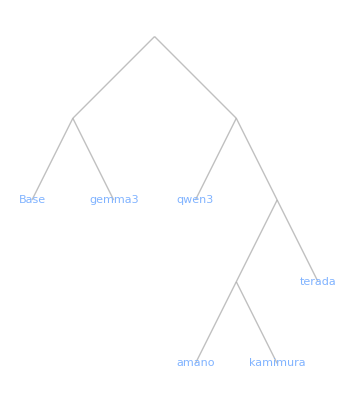

```mathematica
ClusteringTree[data->displayname,DistanceFunction->HammingDistance]
```

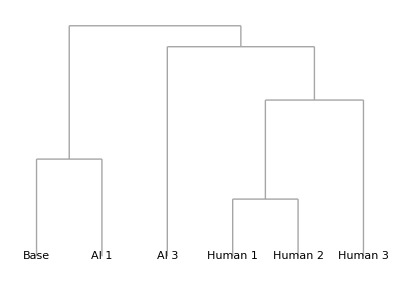

```mathematica
dg=Dendrogram[data->(displayname/.renamerl),DistanceFunction->HammingDistance,ImageSize->400]
```

```mathematica
(*Export[exportdocdir<>"dg.eps",dg,"EPS"]*)
```

```mathematica
hammd=TableForm[Prepend[DistanceMatrix[data,DistanceFunction->HammingDistance],displayname/.renamerl],TableAlignments->Right]
```

Base | AI 1 | Human 1 | Human 2 | Human 3 | AI 3
0 | 51 | 127 | 127 | 141 | 121
51 | 0 | 142 | 136 | 156 | 137
127 | 142 | 0 | 30 | 84 | 123
127 | 136 | 30 | 0 | 82 | 110
141 | 156 | 84 | 82 | 0 | 120
121 | 137 | 123 | 110 | 120 | 0

```mathematica
Export[exportdocdir<>"tab_hammd.txt",hammd,"TeXFragment"]
```

/Volumes/LaCie/BANK/_KAKEN/jsik-cls/tab_hammd.txt

```mathematica
30/415//N
156/415//N
```

0.0722892

0.375904

判定結果の値だけでクラスタリング

元データを削除した判定結果だけの構成を作る

```mathematica
(jsonomportmergeGatherbytxtfineSample=Map[#[[2;;]]&,jsonomportmergeGatherbytxtfine])//Dimensions
```

{99,5,2}

```mathematica
(clusterVal=Transpose[Map[#[[2]]&,jsonomportmergeGatherbytxtfineSample,{2}]])//Dimensions
```

{5,99}

```mathematica
(clusterValJoin=Map[Flatten[Join[#]]&,clusterVal])//Dimensions
```

{5,415}

サンプル名だけにする

```mathematica
(clusterName=Transpose[Map[#[[1]]&,jsonomportmergeGatherbytxtfineSample,{2}]])//Dimensions
```

{5,99}

```mathematica
Map[#[[1]]&,clusterName]
```

{36.ab.txt.gemma3.tail.json,36.ab.txt.h.amano,36.ab.txt.h.kamimura,36.ab.txt.h.terada,36.ab.txt.qwen3.tail.json}

```mathematica
clusterexamplerName={"gemma3","amano","kamimura","terada","qwen3"}
```

{gemma3,amano,kamimura,terada,qwen3}

クラスタリング

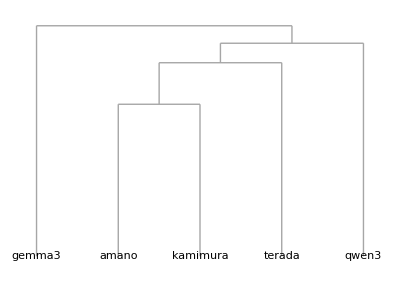

```mathematica
Dendrogram[clusterValJoin->clusterexamplerName,DisplayFunction->HammingDistance]
```

### 修正の程度

どの程度の修正があるのか？

```mathematica
Map[Count[#,0]&,data]
Map[Count[#,0.]&,data]
```

{0,28,127,127,141,95}

{0,0,0,0,0,0}

```mathematica
Map[Count[#,0]&,data]/415//N
Map[Count[#,0.]&,data]/415
```

{0.,0.0674699,0.306024,0.306024,0.339759,0.228916}

{0,0,0,0,0,0}

大学間で判定に差があるのか？

差がなければ地名抽出結果を相対的評価には使える可能性がある。

大学ごとのデータに分ける（判定者はミックスされる）

```mathematica
(U36data=Cases[jsonomportmergeGatherbytxtfineSample,{{x_/;StringMatchQ[x,"36*"],_List},_List,_List,_List,_List}])//Length
```

26

```mathematica
(U41data=Cases[jsonomportmergeGatherbytxtfineSample,{{x_/;StringMatchQ[x,"41*"],_List},_List,_List,_List,_List}])//Length
```

17

```mathematica
(U52data=Cases[jsonomportmergeGatherbytxtfineSample,{{x_/;StringMatchQ[x,"52*"],_List},_List,_List,_List,_List}])//Length
```

31

```mathematica
(U76data=Cases[jsonomportmergeGatherbytxtfineSample,{{x_/;StringMatchQ[x,"76*"],_List},_List,_List,_List,_List}])//Length
```

25

```mathematica
TableForm[{{"大学 1",Length[U36data]},{"大学 2",Length[U41data]},{"大学 3",Length[U52data]},{"大学 4",Length[U76data]}}]
```

大学 1 | 26
大学 2 | 17
大学 3 | 31
大学 4 | 25

```mathematica
U36dataVal=Flatten[Map[#[[2]]&,U36data,{2}],1];
U41dataVal=Flatten[Map[#[[2]]&,U41data,{2}],1];
U52dataVal=Flatten[Map[#[[2]]&,U52data,{2}],1];
U76dataVal=Flatten[Map[#[[2]]&,U76data,{2}],1];
```

修正の程度（ドキュメントごとにどのくらい0が付与されたか）を見る

```mathematica
failratio[x_]:=(Count[x,0]+Count[x,0.])/Length[x]
```

```mathematica
U36dataValfr=Map[failratio,U36dataVal]//N
U41dataValfr=Map[failratio,U41dataVal]//N
U52dataValfr=Map[failratio,U52dataVal]//N
U76dataValfr=Map[failratio,U76dataVal]//N
```

{0.,0.,0.,0.,0.,0.,1.,1.,1.,0.,0.25,0.75,0.75,0.25,0.75,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.333333,0.666667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.,0.,0.,0.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.714286,0.142857,0.142857,0.142857,0.,0.666667,0.666667,0.666667,0.666667,0.5,0.666667,0.166667,0.166667,0.,0.333333,0.,0.227273,0.318182,0.181818,0.272727,0.,0.,0.,0.333333,0.666667,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.,0.,0.5,0.5,0.5,0.5,0.,0.,0.5,0.5,0.5,0.,0.125,0.125,0.9375,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.333333,0.333333,0.333333,0.333333,0.333333,0.666667,0.,0.,0.,0.,0.,0.25,0.25,0.25,0.25,0.25,0.5,0.5,0.5,0.5,0.,0.,1.,0.75,1.,0.,0.,0.2,0.2,0.133333,0.,0.,0.4,0.,0.4,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.5,1.,0.,0.2,0.2,0.,0.4,0.,0.,0.,0.,0.,0.,1.,1.,1.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.}

{0.,1.,0.,1.,0.,0.666667,1.,1.,1.,1.,0.,0.,0.,0.,0.333333,0.,0.75,0.75,0.75,0.,0.,0.5,0.5,0.5,0.,0.,0.142857,0.142857,0.285714,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.4,0.4,0.2,0.4,0.,0.,0.,0.,0.,0.,0.333333,0.333333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.75,0.,0.,1.,1.,1.,1.,0.,0.5,0.5,0.,0.5,0.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.769231,0.769231,0.,0.,0.,0.,0.,0.,0.875,1.,1.,1.,0.,1.,1.,1.,1.,0.,0.666667,0.666667,0.666667,0.666667,0.25,0.,0.25,0.25,0.5,0.,1.,1.,1.,0.,0.,0.25,0.25,0.25,0.5,0.,0.333333,0.333333,0.333333,0.333333,0.,1.,1.,0.,0.,0.5,0.5,0.5,0.5,0.25,0.,0.5,0.5,0.,0.}

{0.,0.,0.,0.,0.,0.,1.,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.8,0.4,0.8,0.2,0.,0.555556,0.444444,0.444444,0.444444,0.,1.,1.,1.,0.,0.,0.,0.,0.,0.125,0.,0.5,0.5,0.5,0.,0.25,0.,0.,0.,0.,0.,0.222222,0.444444,0.222222,0.222222,0.5,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.6,1.,0.8,0.4,0.,1.,1.,1.,0.,0.,1.,1.,1.,0.,0.,0.25,0.25,0.25,0.25,0.,0.166667,0.166667,0.25,0.166667,0.,0.,0.,0.,0.,0.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.2,0.2,0.6,0.2,0.2,0.,0.0909091,0.181818,0.181818,0.272727,0.,1.,1.,0.,0.,0.,1.,1.,1.,0.,0.,0.666667,0.666667,0.666667,0.333333}

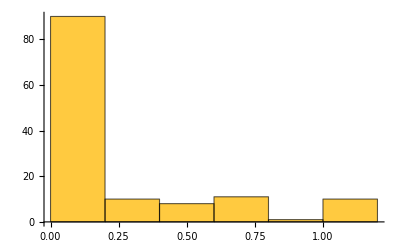
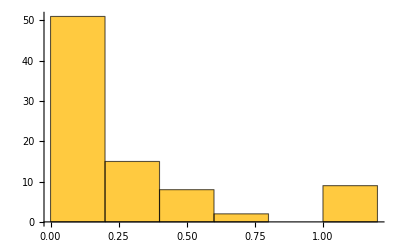
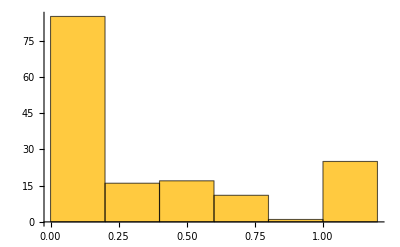
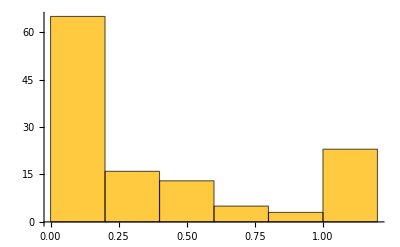
-Graphics-
大学 1 | -Graphics-
大学 2
-Graphics-
大学 3 | -Graphics-
大学 4

```mathematica
Grid[{{TableForm[{U36dataValfr//Histogram,"大学 1"},TableAlignments->Center],
TableForm[{U41dataValfr//Histogram,"大学 2"},TableAlignments->Center]},
{TableForm[{U52dataValfr//Histogram,"大学 3"},TableAlignments->Center],
TableForm[{U76dataValfr//Histogram,"大学 4"},TableAlignments->Center]}}]
```

```mathematica
(*Export[exportdocdir<>"hst1.eps",Histogram[U36dataValfr,ImageSize->400],"EPS"]
Export[exportdocdir<>"hst2.eps",Histogram[U41dataValfr,ImageSize->400],"EPS"]
Export[exportdocdir<>"hst3.eps",Histogram[U52dataValfr,ImageSize->400],"EPS"]
Export[exportdocdir<>"hst4.eps",Histogram[U76dataValfr,ImageSize->400],"EPS"]*)
```

Kruskal-Wallis法を使い複数グループ検定を行う

```mathematica
LocationEquivalenceTest[{U36dataValfr,U41dataValfr,U52dataValfr,U76dataValfr},{"TestDataTable",All}]
```

LocationEquivalenceTest::nvldtst: 与えられた仮定では，有効な検定が見付かりませんでした．KruskalWallis検定を使用しますが，信頼できない結果が得られる可能性があります．

| Statistic | P-Value
Kruskal-Wallis | 9.01328 | 0.0286275

有意差は検出されないが差がないとは見なせないレベル。

### どのような地名が抽出されているのか

2AI,3humanの多数決判定：

```mathematica
majour[l_]:=SortBy[Tally[l],#[[2]]&]//Last//First
```

```mathematica
majorityJudge[org_]:=Module[{namestr,apnd},
namestr=org[[1,1]];
apnd=Map[majour,Transpose[Map[#[[2]]&,org[[2;;]]]]];
Append[org,{namestr<>".majority",apnd}]
]
```

```mathematica
(jsonomportmergeGatherbytxtfinewithM=Map[majorityJudge,jsonomportmergeGatherbytxtfine])//Dimensions
```

{99,7,2}

各大学の元データを抽出する：

```mathematica
(base=Map[#[[1]]&,jsonomportmergeGatherbytxtfinewithM])//Dimensions
```

{99,2}

mecabによる地名秀出の延数・ユニーク数

```mathematica
Map[#[[2]]&,base]//Flatten//Length
Map[#[[2]]&,base]//Flatten//Union//Length
```

415

141

```mathematica
(U36base=Cases[base,{x_/;StringMatchQ[x,"36*"],y_List}])//Length
```

26

```mathematica
(U41base=Cases[base,{x_/;StringMatchQ[x,"41*"],y_List}])//Length
```

17

```mathematica
(U52base=Cases[base,{x_/;StringMatchQ[x,"52*"],y_List}])//Length
```

31

```mathematica
(U76base=Cases[base,{x_/;StringMatchQ[x,"76*"],y_List}])//Length
```

25

各大学判定結果を抽出する：

```mathematica
(judge=Map[#[[7]]&,jsonomportmergeGatherbytxtfinewithM])//Dimensions
```

{99,2}

```mathematica
(U36judge=Cases[judge,{x_/;StringMatchQ[x,"36*"],y_List}])//Length
```

26

```mathematica
(U41judge=Cases[judge,{x_/;StringMatchQ[x,"41*"],y_List}])//Length
```

17

```mathematica
(U52judge=Cases[judge,{x_/;StringMatchQ[x,"52*"],y_List}])//Length
```

31

```mathematica
(U76judge=Cases[judge,{x_/;StringMatchQ[x,"76*"],y_List}])//Length
```

25

地名が出現した報告書数

```mathematica
Cases[U36judge,{_String,{___,__String,___}}]//Length
Cases[U41judge,{_String,{___,__String,___}}]//Length
Cases[U52judge,{_String,{___,__String,___}}]//Length
Cases[U76judge,{_String,{___,__String,___}}]//Length
```

24

15

26

19

```mathematica
TableForm[{{"大学 1","24/26"},
{"大学 2","15/17"},
{"大学 3","26/31"},
{"大学 4","19/25"}
},TableHeadings->{None, {"大学","地名が出現した\n報告書数"}}]
```

大学 | 地名が出現した
報告書数
大学 1 | 24/26
大学 2 | 15/17
大学 3 | 26/31
大学 4 | 19/25

```mathematica
TableForm[{{"大学 1","24/26"},
{"大学 2","15/17"},
{"大学 3","26/31"},
{"大学 4","19/25"}
}]
```

大学 1 | 24/26
大学 2 | 15/17
大学 3 | 26/31
大学 4 | 19/25

```mathematica
Flatten[Map[#[[2]]&,U36base]]//Union
```

{中,亘,周,境,成,日,曽,集,ポー,下条,中国,京都,兵庫,内保,北京,台湾,四川,埼玉,富士,山梨,岐阜,日本,早川,東京,東海,欧州,甲州,甲府,福生,笹子,筑波,荒川,西安,赤沢,長野,ローマ,北海道,富士川,東日本,武蔵野,イタリア,フランス,ベトナム,ボローニャ}

```mathematica
U36chimeiTly=SortBy[Cases[Flatten[Map[#[[2]]&,U36judge]],_String]//Tally,Last]//Reverse
```

{{山梨,26},{日本,8},{イタリア,7},{甲州,6},{甲府,5},{ベトナム,3},{四川,3},{中国,3},{ボローニャ,2},{荒川,2},{富士,2},{台湾,2},{フランス,1},{武蔵野,1},{富士川,1},{北海道,1},{ローマ,1},{長野,1},{赤沢,1},{西安,1},{筑波,1},{笹子,1},{欧州,1},{東海,1},{東京,1},{早川,1},{岐阜,1},{埼玉,1},{北京,1},{兵庫,1},{京都,1},{集,1}}

```mathematica
U36chimei=Complement[Map[#[[2]]&,U36judge]//Flatten//Union,{0,0.}]
```

{集,中国,京都,兵庫,北京,台湾,四川,埼玉,富士,山梨,岐阜,日本,早川,東京,東海,欧州,甲州,甲府,笹子,筑波,荒川,西安,赤沢,長野,ローマ,北海道,富士川,武蔵野,イタリア,フランス,ベトナム,ボローニャ}

```mathematica
Flatten[Map[#[[2]]&,U41base]]//Union
```

{亜,加,成,日,栄,独,米,纒,一山,中京,佐渡,八戸,大阪,奥津,富山,山口,岡山,広島,志賀,日本,東京,珠洲,石川,能登,苫田,金沢,長崎,青森,アジア,京阪神,小笠原,ヨルダン,ウラジオストク,オーストラリア}

```mathematica
U41chimeiTly=SortBy[Cases[Flatten[Map[#[[2]]&,U41judge]],_String]//Tally,Last]//Reverse
```

{{金沢,9},{東京,4},{八戸,4},{石川,3},{奥津,3},{ウラジオストク,2},{アジア,2},{青森,2},{能登,2},{珠洲,2},{日本,2},{志賀,2},{広島,2},{岡山,2},{大阪,2},{米,2},{オーストラリア,1},{ヨルダン,1},{京阪神,1},{長崎,1},{苫田,1},{富山,1},{佐渡,1},{中京,1},{一山,1},{独,1}}

```mathematica
U41chimei=Complement[Map[#[[2]]&,U41judge]//Flatten//Union,{0,0.}]
```

{独,米,一山,中京,佐渡,八戸,大阪,奥津,富山,岡山,広島,志賀,日本,東京,珠洲,石川,能登,苫田,金沢,長崎,青森,アジア,京阪神,ヨルダン,ウラジオストク,オーストラリア}

```mathematica
Flatten[Map[#[[2]]&,U52base]]//Union
```

{仏,加,周,日,求,米,継,英,起,離,韓,佐賀,北欧,大阪,安土,愛知,日内,日本,極北,欧米,滋賀,神戸,稲津,米国,草津,韓国,高島,インド,フランス,ベルゲン,フィンランド,ATP,S}

```mathematica
U52chimeiTly=SortBy[Cases[Flatten[Map[#[[2]]&,U52judge]],_String]//Tally,Last]//Reverse
```

{{滋賀,20},{日,10},{高島,5},{日本,5},{米,5},{草津,4},{米国,4},{佐賀,3},{仏,3},{S,1},{フィンランド,1},{フランス,1},{インド,1},{韓国,1},{神戸,1},{欧米,1},{極北,1},{愛知,1},{安土,1},{大阪,1},{北欧,1},{韓,1},{英,1}}

```mathematica
U52chimei=Complement[Map[#[[2]]&,U52judge]//Flatten//Union,{0,0.}]
```

{仏,日,米,英,韓,佐賀,北欧,大阪,安土,愛知,日本,極北,欧米,滋賀,神戸,米国,草津,韓国,高島,インド,フランス,フィンランド,S}

```mathematica
Flatten[Map[#[[2]]&,U76base]]//Union
```

{仏,成,日,泰,津,清,独,米,英,豪,集,静,ネス,中国,中央,中野,丹後,久山,九州,京都,仙台,佐伯,備後,元岡,南部,四川,土井,大阪,宮谷,平戸,彦沢,日本,東京,欧州,毛利,沖縄,滋賀,熊本,生葉,白川,的場,福岡,米国,芦生,英国,長崎,韓国,アジア,ドイツ,久留米,千代田,大学北,太平洋,有楽町,琵琶湖,アメリカ,ホノルル,大韓民国,ワシントン,マンチェスター}

```mathematica
U76chimeiTly=SortBy[Cases[Flatten[Map[#[[2]]&,U76judge]],_String]//Tally,Last]//Reverse
```

{{日本,11},{米,10},{福岡,8},{日,8},{アジア,4},{九州,4},{中国,4},{ドイツ,3},{米国,3},{平戸,3},{仙台,3},{久山,3},{独,3},{太平洋,2},{東京,2},{大阪,2},{南部,2},{大韓民国,1},{ホノルル,1},{アメリカ,1},{有楽町,1},{千代田,1},{久留米,1},{韓国,1},{長崎,1},{英国,1},{芦生,1},{白川,1},{熊本,1},{滋賀,1},{沖縄,1},{欧州,1},{四川,1},{備後,1},{佐伯,1},{中央,1},{豪,1},{英,1},{津,1},{仏,1}}

```mathematica
U76chimei=Complement[Map[#[[2]]&,U76judge]//Flatten//Union,{0,0.}]
```

{仏,日,津,独,米,英,豪,中国,中央,久山,九州,仙台,佐伯,備後,南部,四川,大阪,平戸,日本,東京,欧州,沖縄,滋賀,熊本,白川,福岡,米国,芦生,英国,長崎,韓国,アジア,ドイツ,久留米,千代田,太平洋,有楽町,アメリカ,ホノルル,大韓民国}

決定地名：

```mathematica
TableForm[{{U36chimeiTly,U41chimeiTly,U52chimeiTly,U76chimeiTly}},TableHeadings->{None, {"大学 1","大学 2","大学 3","大学 4"}},TableAlignments->{Left, Top}]
```

大学 1 | 大学 2 | 大学 3 | 大学 4
山梨 | 26
日本 | 8
イタリア | 7
甲州 | 6
甲府 | 5
ベトナム | 3
四川 | 3
中国 | 3
ボローニャ | 2
荒川 | 2
富士 | 2
台湾 | 2
フランス | 1
武蔵野 | 1
富士川 | 1
北海道 | 1
ローマ | 1
長野 | 1
赤沢 | 1
西安 | 1
筑波 | 1
笹子 | 1
欧州 | 1
東海 | 1
東京 | 1
早川 | 1
岐阜 | 1
埼玉 | 1
北京 | 1
兵庫 | 1
京都 | 1
集 | 1 | 金沢 | 9
東京 | 4
八戸 | 4
石川 | 3
奥津 | 3
ウラジオストク | 2
アジア | 2
青森 | 2
能登 | 2
珠洲 | 2
日本 | 2
志賀 | 2
広島 | 2
岡山 | 2
大阪 | 2
米 | 2
オーストラリア | 1
ヨルダン | 1
京阪神 | 1
長崎 | 1
苫田 | 1
富山 | 1
佐渡 | 1
中京 | 1
一山 | 1
独 | 1 | 滋賀 | 20
日 | 10
高島 | 5
日本 | 5
米 | 5
草津 | 4
米国 | 4
佐賀 | 3
仏 | 3
S | 1
フィンランド | 1
フランス | 1
インド | 1
韓国 | 1
神戸 | 1
欧米 | 1
極北 | 1
愛知 | 1
安土 | 1
大阪 | 1
北欧 | 1
韓 | 1
英 | 1 | 日本 | 11
米 | 10
福岡 | 8
日 | 8
アジア | 4
九州 | 4
中国 | 4
ドイツ | 3
米国 | 3
平戸 | 3
仙台 | 3
久山 | 3
独 | 3
太平洋 | 2
東京 | 2
大阪 | 2
南部 | 2
大韓民国 | 1
ホノルル | 1
アメリカ | 1
有楽町 | 1
千代田 | 1
久留米 | 1
韓国 | 1
長崎 | 1
英国 | 1
芦生 | 1
白川 | 1
熊本 | 1
滋賀 | 1
沖縄 | 1
欧州 | 1
四川 | 1
備後 | 1
佐伯 | 1
中央 | 1
豪 | 1
英 | 1
津 | 1
仏 | 1

Baseターム：

```mathematica
Map[#[[2]]&,base]//Flatten//Union//Length
```

141

地名であると判断されたターム：

```mathematica
Union[U36chimei,U41chimei,U52chimei,U76chimei]//Length
```

99

```mathematica
Union[U36chimei,U41chimei,U52chimei,U76chimei]
```

{仏,日,津,独,米,英,豪,集,韓,一山,中京,中国,中央,久山,九州,京都,仙台,佐伯,佐渡,佐賀,備後,八戸,兵庫,北京,北欧,南部,台湾,四川,埼玉,大阪,奥津,安土,富士,富山,山梨,岐阜,岡山,平戸,広島,志賀,愛知,日本,早川,東京,東海,極北,欧州,欧米,沖縄,滋賀,熊本,珠洲,甲州,甲府,白川,石川,神戸,福岡,笹子,筑波,米国,能登,芦生,苫田,英国,草津,荒川,西安,赤沢,金沢,長崎,長野,青森,韓国,高島,アジア,インド,ドイツ,ローマ,久留米,京阪神,北海道,千代田,太平洋,富士川,有楽町,武蔵野,アメリカ,イタリア,フランス,ベトナム,ホノルル,ヨルダン,大韓民国,ボローニャ,フィンランド,ウラジオストク,オーストラリア,S}

地名でないと判定されたターム：

```mathematica
U36notchimei=Complement[Map[#[[2]]&,U36base]//Flatten,Map[#[[2]]&,U36judge]//Flatten]
U41notchimei=Complement[Map[#[[2]]&,U41base]//Flatten,Map[#[[2]]&,U41judge]//Flatten]
U52notchimei=Complement[Map[#[[2]]&,U52base]//Flatten,Map[#[[2]]&,U52judge]//Flatten]
U76notchimei=Complement[Map[#[[2]]&,U76base]//Flatten,Map[#[[2]]&,U76judge]//Flatten]
```

{中,亘,周,境,成,日,曽,ポー,下条,内保,福生,東日本}

{亜,加,成,日,栄,纒,山口,小笠原}

{加,周,求,継,起,離,日内,稲津,ベルゲン,ATP}

{成,泰,清,集,静,ネス,中野,丹後,京都,元岡,土井,宮谷,彦沢,毛利,生葉,的場,大学北,琵琶湖,ワシントン,マンチェスター}

```mathematica
Union[U36notchimei,U41notchimei,U52notchimei,U76notchimei]
```

{中,亘,亜,加,周,境,成,日,曽,栄,求,泰,清,継,纒,起,集,離,静,ネス,ポー,下条,中野,丹後,京都,元岡,内保,土井,宮谷,山口,彦沢,日内,毛利,生葉,的場,福生,稲津,大学北,小笠原,東日本,琵琶湖,ベルゲン,ワシントン,マンチェスター,ATP}

地名であると判定された場合も地名でないと判定された場合もあるターム：

```mathematica
Intersection[Union[U36notchimei,U41notchimei,U52notchimei,U76notchimei],Union[U36chimei,U41chimei,U52chimei,U76chimei]]
```

{日,集,京都}

地名でないと判断されたタームは、ほとんどが史料名、組織名、条約名等の一部であり、単独で地名でないと判断できるものは非常に少ない。

大学ごとに出現する地名にどの程度異なりがあるか？（地名と判断されたもの）

ダイス係数のクロス表（重なりを見ている）

```mathematica
dice[a_,b_]:=2Length[Intersection[a,b]]/(Length[a]+Length[b])
```

```mathematica
Round[Outer[dice,{U36chimei,U41chimei,U52chimei,U76chimei},{U36chimei,U41chimei,U52chimei,U76chimei},1]//N,0.01]//TableForm
```

1. | 0.07 | 0.07 | 0.14
0.07 | 1. | 0.12 | 0.21
0.07 | 0.12 | 1. | 0.29
0.14 | 0.21 | 0.29 | 1.

あまり重なりはなく、特徴が表れていると言えなくもないが、サンプリング数が少ない可能性もある。